```mathematica
Needs["MaTeX`"];
(*PREDEFINED LABEL STYLE*)
labstyle={FontFamily->"Latin Modern Roman",FontSize->20};
magn=2;
IS=400;
thick=0.008;
thin=0.006;
dash={0.015,0.02};
pointsize=0.03;
(*Remove In/Out*)
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];

(*decomposition code*)
(*Define Pauli matrices*)σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
id=IdentityMatrix[2];
(*Labels and matrices*)
pauliLabels={"I","σx","σy","σz"};
pauliMatrices={id,σx,σy,σz};

(*decomposition of 2 spins*)
n=2;
(*Generate all combinations*)
tuples=Tuples[Range[4],n];(*1-based indexing*)basisOps=KroneckerProduct@@@(pauliMatrices[[#]]&/@tuples);
basisLabels=StringRiffle[pauliLabels[[#]]&/@#," ⊗ "]&/@tuples;

(*Count number of non-identity terms*)
nonIdentityCounts=Count[#,x_/;x!=1]&/@tuples;
decompose1d[M_] := Tr[M. #]/2 & /@ {σx, σz}; (*a shorter single qubit decomp*)

(*Decomposition function*)
DecomposeSpinOperators[M_]:=Module[{coeffs,assoc,filtered},coeffs=Table[Tr[ConjugateTranspose[b].M]/8//FullSimplify,{b,basisOps}];
assoc=AssociationThread[Transpose[{basisLabels,nonIdentityCounts}]->coeffs];
filtered=Select[assoc,Chop[#]=!=0&];
<|"SingleQubitTerms"->KeySelect[filtered,#[[2]]==1&],"TwoQubitTerms"->KeySelect[filtered,#[[2]]==2&],"ThreeQubitTerms"->KeySelect[filtered,#[[2]]==3&]|>]
```

## 1 XOSO

```mathematica
(*set paramters*)
pars={
θ1->0.3,θ2->0.3,
g1->59,g2->74,g3->47(*MHz*)
(*J->1*)
}
n1={0,1,0};
n2={0,1,0};

j1arr=Table[x,{x,0.2,150,0.5}];
j2arr=Table[x,{x,0.2,150,0.5}];  (*scan J in MHz*)

(*Define Hamiltonians*)
Rot1=RotationMatrix[θ1,n1//Normalize];
Rot2=RotationMatrix[θ2,n2//Normalize];
B0=(g1+g2+g3)/3/.pars;
j1arr=j1arr/B0;
j2arr=j2arr/B0;
Hmat= 1/(2 B0)(g1  KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+ g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+ g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+1/4 Sum[j1 Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+j2 Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars//FullSimplify;
Hdj=1/4 Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]-Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars;
HΣj=1/4 Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars;

Hj1=1/4 Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]/.pars;
Hj2=1/4 Sum[Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars;
(*Eigenvalues*)
X=ParallelTable[(Sort@Transpose@Eigensystem[Hmat])ᵀ,{j1,j1arr},{j2,j2arr}];//AbsoluteTiming
eigval=X[[;;,;;,1]]; 
eigvect=X[[;;,;;,2]];
(*plot gap*)
pi=Flatten[Table[{j1arr[[i]],j2arr[[j]],Log10[eigval[[i,j,3]]-eigval[[i,j,2]]]}ᵀ,{i, 1, Length[j1arr]},{j, 1, Length[j2arr]}],1];
ListDensityPlot[pi,Frame->True,PlotRange->{-10,1},
ColorFunction->"TemperatureMap",
LabelStyle->labstyle,
FrameLabel->{
MaTeX["J_1/\\bar{b}", Magnification -> magn] ,
MaTeX[" J_2/\\bar{b}", Magnification ->magn],
MaTeX["\\log_{10}(E_3 - E_2)", Magnification -> magn]
},
PlotLegends->Automatic,
ImageSize->IS
]
```

{θ1→0.3,θ2→0.3,g1→59,g2→74,g3→47}

{147.322,Null}

-Graphics-

```mathematica
SZop=Plus@@KroneckerProduct@@@Permutations[{σz,id,id}]/2;
```

{300,8,8}

```mathematica
(*Plot energy*)
(*
Manipulate[
pi=Table[{Barr,eigval[[;;,dj,n]]}ᵀ,{n,1,8}];
GraphicsRow[{
ListLinePlot[pi,Frame->True,
FrameLabel->{MaTeX["\\bar{b}/\\bar{J}", Magnification -> magn] ,MaTeX[" \\epsilon/\\bar{J}", Magnification -> magn]},
ImageSize->2IS,
Frame->True,LabelStyle->labstyle],
ListLinePlot[{pi[[1]],pi[[2]]},Frame->True,PlotRange->{0,0.3},
FrameLabel->{MaTeX["\\bar{b}/\\bar{J}", Magnification -> magn] ,MaTeX[" \\epsilon/\\bar{J}", Magnification -> magn]},
ImageSize->2IS,
Frame->True,
LabelStyle->labstyle
], StringJoin["δJ/J=",ToString[δjarr[[dj]]//N]]
},ImageSize->2IS],
{dj,1,Length[δjarr],1}
]*)
```

Transpose::nmtx: The first two levels of {Barr,{-1.49835,-1.4963,-1.49424,-1.49218,-1.49013,-1.48808,«39»,-1.40813,-1.40621,-1.4043,-1.40239,-1.40049,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.689661,-0.687604,-0.685549,-0.683495,-0.681442,-0.679392,«39»,-0.760189,-0.765236,-0.770309,-0.775407,-0.780527,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.586215,-0.588363,-0.590608,-0.592952,-0.595392,-0.597929,«40»,-0.597552,-0.59564,-0.593733,-0.591833,«250»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Barr,{-1.49835,-1.4963,-1.49424,-1.49218,-1.49013,-1.48808,«40»,-1.40621,-1.4043,-1.40239,-1.40049,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.689661,-0.687604,-0.685549,-0.683495,-0.681442,-0.679392,«40»,-0.765236,-0.770309,-0.775407,-0.780527,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.586215,-0.588363,-0.590608,-0.592952,-0.595392,-0.597929,«40»,-0.597552,-0.59564,-0.593733,-0.591833,«250»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Barr,{-1.49841,-1.49642,-1.49443,-1.49244,-1.49046,-1.48848,«40»,-1.40912,-1.40725,-1.40539,-1.40354,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.716673,-0.714684,-0.712697,-0.710711,-0.708727,-0.706744,«40»,-0.709048,-0.71437,-0.719709,-0.725063,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.516678,-0.518788,-0.521032,-0.523407,-0.525914,-0.528549,«40»,-0.627404,-0.625541,-0.623682,-0.621829,«250»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Barr,{-1.49841,-1.49642,-1.49443,-1.49244,-1.49046,«41»,-1.40912,-1.40725,-1.40539,-1.40354,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.716673,-0.714684,-0.712697,-0.710711,-0.708727,-0.706744,«40»,-0.709048,-0.71437,-0.719709,-0.725063,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{-0.516678,-0.518788,-0.521032,-0.523407,-0.525914,-0.528549,«40»,-0.627404,-0.625541,-0.623682,-0.621829,«250»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,«23»,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,«24»,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{ImageSize}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

MaTeX::invopt: Invalid option value: Magnification→magn.

General::stop: Further output of MaTeX::invopt will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,«8»,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,«9»,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{«9»}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{ImageSize}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

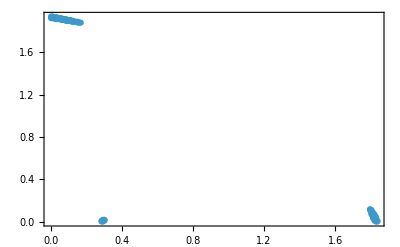

```mathematica
δe=eigval[[;;,;;,3]]-eigval[[;;,;;,2]];
ths=10^-2;
pos=Position[Chop[δe,ths],0];
curve=Table[{j1arr[[pos[[i,1]]]],j2arr[[pos[[i,2]]]]},{i,1,Dimensions[pos][[1]]}];
ListPlot[curve,
Frame->True,
LabelStyle->labstyle,
FrameLabel->{
MaTeX["J_1/\\bar{b}", Magnification -> magn] ,
MaTeX[" J_2/\\bar{b}", Magnification ->magn]
},
PlotLegends->Automatic,
ImageSize->IS]
```

```mathematica
(*Find position and effective theory of TMS*)

δe=eigval[[;;,;;,3]]-eigval[[;;,;;,2]];
ths=10^-2;
pos=Position[Chop[δe,ths],0];
curve=Table[{j1arr[[pos[[i,1]]]],j2arr[[pos[[i,2]]]]},{i,1,Dimensions[pos][[1]]}];
ListPlot[curve,
Frame->True,
LabelStyle->labstyle,
FrameLabel->{
MaTeX["J_1/\\bar{b}", Magnification -> magn] ,
MaTeX[" J_2/\\bar{b}", Magnification ->magn]
},
PlotLegends->Automatic,
ImageSize->IS]

itest=85;

h0=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hmat.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ/.{j1->curve[[itest,1]],j2->curve[[itest,2]]};
hj1=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hj1.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ//Chop;
hj2=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hj2.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ//Chop;
h0=h0-(h0[[1,1]]+h0[[2,2]])/2 IdentityMatrix[2]//FullSimplify;
hj1=hj1-(hj1[[1,1]]+hj1[[2,2]])/2 IdentityMatrix[2];
hj2=hj2-(hj2[[1,1]]+hj2[[2,2]])/2 IdentityMatrix[2];
Hxoso=h0+hj1 j1+hj2 j2//Chop//FullSimplify//MatrixForm

eigvect[[pos[[itest,1]],pos[[itest,2]],3]]*.SZop.eigvect[[pos[[itest,1]],pos[[itest,2]],3]]ᵀ
eigvect[[pos[[itest,1]],pos[[itest,2]],2]]*.SZop.eigvect[[pos[[itest,1]],pos[[itest,2]],2]]ᵀ
{j1arr[[pos[[itest,1]]]],j2arr[[pos[[itest,2]]]]}
```

-Graphics-

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

Thread::tdlen: Objects of unequal length in Times[<<1095092216 bytes>>] cannot be combined.

Thread::tdlen: Objects of unequal length in Times[<<1095092240 bytes>>] cannot be combined.

$Aborted

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

Part::partw: Part 87 of {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},{6,230},«22»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»} does not exist.

$Aborted[]

Part::pkspec1: The expression {{1,231},{1,232},{1,233},{2,231},{2,232},{2,233},{3,231},{3,232},{4,230},{4,231},{4,232},{5,230},{5,231},{5,232},«23»,{16,228},{17,227},{18,227},{19,226},{19,227},{20,226},{21,226},{35,1},{35,2},{36,1},{36,2},{36,3},{37,2},«32»}⟦87,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in Times[<<1417548064 bytes>>] cannot be combined.

Thread::tdlen: Objects of unequal length in Times[<<1417548088 bytes>>] cannot be combined.

```mathematica
(*to see the angles of sigmax sigmaz*)
```

```mathematica
(*anglesFromCoeffs[vec_]:=(VectorAngle[{Coefficient[#,j1],Coefficient[#,j2]},{1,0}]&/@vec)/Degree;
Manipulate[ Quiet[
itest=it;
h0=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hmat.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ/.{j1->curve[[itest,1]],j2->curve[[itest,2]]};
hj1=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hj1.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ//Chop;
hj2=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hj2.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ//Chop;
h0=h0-(h0[[1,1]]+h0[[2,2]])/2 IdentityMatrix[2]//FullSimplify;
hj1=hj1-(hj1[[1,1]]+hj1[[2,2]])/2 IdentityMatrix[2];
hj2=hj2-(hj2[[1,1]]+hj2[[2,2]])/2 IdentityMatrix[2];

{curve[[it]],Hxoso=h0+hj1 j1+hj2 j2//Chop//FullSimplify//MatrixForm,decompose1d[First[Hxoso]]//FullSimplify}],
{it,1,Dimensions[pos][[1]],1}]
(*to see the angles of sigmax sigmaz*)
Manipulate[Quiet[
itest=it;
h0=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hmat.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ/.{j1->curve[[itest,1]],j2->curve[[itest,2]]};
hj1=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hj1.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ//Chop;
hj2=eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]*.Hj2.eigvect[[pos[[itest,1]],pos[[itest,2]],2;;3]]ᵀ//Chop;
h0=h0-(h0[[1,1]]+h0[[2,2]])/2 IdentityMatrix[2]//FullSimplify;
hj1=hj1-(hj1[[1,1]]+hj1[[2,2]])/2 IdentityMatrix[2];
hj2=hj2-(hj2[[1,1]]+hj2[[2,2]])/2 IdentityMatrix[2];
Hxoso=h0+hj1 j1+hj2 j2//Chop//FullSimplify;

{curve[[it]],decompose1d[Hxoso]//FullSimplify//anglesFromCoeffs}],
{it,1,Dimensions[pos][[1]],1}]*)
```

## 2 XOSOs

```mathematica
(*set paramters*)
pars1={θ1->0.0,θ2->0.0,g1->53,g2->74,g3->47(*MHz*)

}
pars2={
θ1->0.0,θ2->0.0,
g1->60,g2->72,g3->43(*MHz*)

(*J->1*)
};
Jexp[g1_,g2_,g3_]:=Module[{M,L,tot},M=g2-g1;L=2*g3-g1-g2;tot=(M^2-L^2)/(2*L)//N];
Jexp[g1,g2,g3]/.pars1 (*this i added to see what the idle exchange value is*)
Jexp[g3,g2,g1]/.pars1
Jexp[g1,g2,g3]/.pars2
Jexp[g3,g2,g1]/.pars2
```

{θ1→0.,θ2→0.,g1→53,g2→74,g3→47}

9.81818

-16.8

21.4348

81.6

```mathematica
parsint={
θint->0.00
}
n1={0,1,0};
n2={0,1,0};
nint={0,1,0};
(*set paramters*)


(*Define Hamiltonians*)
Rot1=RotationMatrix[θ1,n1//Normalize];
Rot2=RotationMatrix[θ2,n2//Normalize];
B0=(((g1+g2+g3)/3/.pars1)+((g1+g2+g3)/3/.pars2))/2//N
j2arr=Table[x,{x,0,0,0.01}];
j1arr=Table[x,{x,0,23,0.002}];  (*scan J in MHz*)
j1arr=j1arr/1;
j2arr=j2arr/1;

(*Define Hamiltonians*)
Rot1=RotationMatrix[θ1,n1//Normalize];
Rot2=RotationMatrix[θ2,n2//Normalize];
Rotint=RotationMatrix[θint,nint//Normalize];
(*Q1*)
Hmat1= 1/(2*1)(g1  KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+ g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+ g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+(1/4)Sum[j1 Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+j2 Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars1//FullSimplify;
Hdj1=(1/4)Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]-Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars1;
HΣj1=(1/4)Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars1;
(*Eigenvalues*)
X=ParallelTable[(Sort@Transpose@Eigensystem[Hmat1])ᵀ,{j1,j1arr},{j2,j2arr}];//AbsoluteTiming
eigval1=X[[;;,;;,1]]-X[[;;,;;,1,1]];
eigvect1=X[[;;,;;,2]];

(*Q2*)
Hmat2= 1/(2 *1)(g1  KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+ g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+ g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+(1/4)Sum[j1 Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+j2 Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars2//FullSimplify;
Hdj2=(1/4)Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]-Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars2;
HΣj2=(1/4)Sum[Rot1[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+Rot2[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}]/.pars2;
(*Eigenvalues*)
X=ParallelTable[(Sort@Transpose@Eigensystem[Hmat2])ᵀ,{j1,j1arr},{j2,j2arr}];//AbsoluteTiming
eigval2=X[[;;,;;,1]]-X[[;;,;;,1,1]];
eigvect2=X[[;;,;;,2]];
(*couplings that cannot be turned on in 343*)
couplings={jcc->0};
(*Interactions*)
Hint=((jcc(1/4)Sum[Rotint[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[0],PauliMatrix[0],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]+
jsc(1/4)Sum[Rotint[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[i],PauliMatrix[0],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]+
jss1(1/4)Sum[Rotint[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[i],PauliMatrix[0],PauliMatrix[0],PauliMatrix[j]],{i,1,3},{j,1,3}]+
jss2(1/4)Sum[Rotint[[i,j]]KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[i],PauliMatrix[j],PauliMatrix[0],PauliMatrix[0]],{i,1,3},{j,1,3}]+
jss3(1/4)Sum[Rotint[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[0],PauliMatrix[0],PauliMatrix[j],PauliMatrix[0],PauliMatrix[0]],{i,1,3},{j,1,3}]+
jss4(1/4)Sum[Rotint[[i,j]]KroneckerProduct[PauliMatrix[i],PauliMatrix[0],PauliMatrix[0],PauliMatrix[0],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]))/.parsint /.couplings;
```

{θint→0.}

58.1667

{1.44268,Null}

{1.37711,Null}

```mathematica
(*Plot energy*)
(*
Print["Q1"]
Manipulate[
pi=Table[{Barr,eigval1[[;;,dj,n]]}ᵀ,{n,1,8}];
GraphicsRow[{
ListLinePlot[pi,Frame->True,
FrameLabel->{MaTeX["\\bar{b}/\\bar{J}", Magnification -> magn] ,MaTeX[" \\epsilon_1/\\bar{J}", Magnification -> magn]},
ImageSize->2IS,
Frame->True,LabelStyle->labstyle],
ListLinePlot[{pi[[1]],pi[[2]]},Frame->True,PlotRange->{0,0.3},
FrameLabel->{MaTeX["\\bar{b}/\\bar{J}", Magnification -> magn] ,MaTeX[" \\epsilon_1/\\bar{J}", Magnification -> magn]},
ImageSize->2IS,
Frame->True,
LabelStyle->labstyle
], StringJoin["δJ/J=",ToString[δjarr[[dj]]//N]]
},ImageSize->2IS],
{dj,1,Length[δjarr],1}
]
Print["Q2"]
Manipulate[
pi=Table[{Barr,eigval2[[;;,dj,n]]}ᵀ,{n,1,8}];
GraphicsRow[{
ListLinePlot[pi,Frame->True,
FrameLabel->{MaTeX["\\bar{b}/\\bar{J}", Magnification -> magn] ,MaTeX[" \\epsilon_2/\\bar{J}", Magnification -> magn]},
ImageSize->2IS,
Frame->True,LabelStyle->labstyle],
ListLinePlot[{pi[[1]],pi[[2]]},Frame->True,PlotRange->{0,0.3},
FrameLabel->{MaTeX["\\bar{b}/\\bar{J}", Magnification -> magn] ,MaTeX[" \\epsilon_2/\\bar{J}", Magnification -> magn]},
ImageSize->2IS,
Frame->True,
LabelStyle->labstyle
], StringJoin["δJ/J=",ToString[δjarr[[dj]]//N]]
},ImageSize->2IS],
{dj,1,Length[δjarr],1}
]*)
```

Q1

Q2

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Options::optnf: ImageSize is not a known option for MapThread[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(Slot[«1»]+MaTeX`Private`$psfactor)/Slot[«1»]]]&,{{},{20.3997},{16.9798},{4.3039}}].

Show::gtype: MapThread is not a type of graphics.

Import::general: Expected cross reference table

Import::general: Could not find document trailer

General::stop: Further output of Import::general will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(Slot[«1»]+MaTeX`Private`$psfactor)/Slot[«1»]]]&,{{},{24.8816},{16.8469},{4.3039}}]; dimensions are 0 and 1.

Options::optnf: ImageSize is not a known option for Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(#4+MaTeX`Private`$psfactor)/#3]]&.

Show::gtype: Function is not a type of graphics.

Options::optnf: ImageSize is not a known option for {{},{24.8816},{16.8469},{4.3039}}.

General::stop: Further output of Options::optnf will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{{},{24.8816},{16.8469},{4.3039}},ImageSize→2. ImageSize].

MapThread::list: List expected at position 2 in MapThread[Show[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[Plus[«2»] Power[«2»]]]&,ImageSize→2. ImageSize],Show[{{},{24.8816},{16.8469},{4.3039}},ImageSize→2. ImageSize]].

Show::gtype: MapThread is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,«10»,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,«12»,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{«9»}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Options::optnf: ImageSize is not a known option for MapThread[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(Slot[«1»]+MaTeX`Private`$psfactor)/Slot[«1»]]]&,{{},{20.3997},{16.9798},{4.3039}}].

Show::gtype: MapThread is not a type of graphics.

Import::general: Expected cross reference table

Import::general: Could not find document trailer

General::stop: Further output of Import::general will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(Slot[«1»]+MaTeX`Private`$psfactor)/Slot[«1»]]]&,{{},{24.8816},{16.8469},{4.3039}}]; dimensions are 0 and 1.

Options::optnf: ImageSize is not a known option for Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(#4+MaTeX`Private`$psfactor)/#3]]&.

Show::gtype: Function is not a type of graphics.

Options::optnf: ImageSize is not a known option for {{},{24.8816},{16.8469},{4.3039}}.

General::stop: Further output of Options::optnf will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{{},{24.8816},{16.8469},{4.3039}},ImageSize→2. ImageSize].

MapThread::list: List expected at position 2 in MapThread[Show[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[Plus[«2»] Power[«2»]]]&,ImageSize→2. ImageSize],Show[{{},{24.8816},{16.8469},{4.3039}},ImageSize→2. ImageSize]].

Show::gtype: MapThread is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,«10»,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,«12»,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{«9»}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Barr,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{0.847642,0.84764,0.847638,0.847635,0.847633,0.84763,«39»,0.677958,0.67067,0.66336,0.656032,0.648686,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{0.954399,0.949993,0.945487,0.940881,0.936176,0.931373,«39»,0.847642,0.84764,0.847638,0.847636,0.847634,«250»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Barr,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{0.773541,0.768997,0.764326,0.759526,0.754601,0.74955,«39»,0.476294,0.468477,0.460643,0.452794,0.444931,«250»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{0.992219,0.992219,0.992218,0.992217,0.992216,0.992215,«39»,0.985509,0.984768,0.984057,0.983378,0.982729,«250»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,«23»,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,«24»,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{ImageSize}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Barr,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11451»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{43.,43.,43.,43.,43.,43.,43.,43.,43.,«33»,43.,43.,43.,43.,43.,43.,43.,43.,«11451»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{60.,59.999,59.998,59.997,59.996,59.995,59.994,59.993,59.992,«33»,59.9579,59.9568,59.9558,59.9548,59.9538,59.9528,59.9518,59.9508,«11451»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Barr,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11451»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{47.,47.,47.,47.,47.,47.,47.,47.,47.,«33»,47.,47.,47.,47.,47.,47.,47.,47.,«11451»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{56.,55.999,55.998,55.997,55.996,55.995,55.994,55.993,55.992,«33»,55.9579,55.9569,55.9559,55.9549,55.9539,55.9529,55.9519,55.9509,«11451»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Barr,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11451»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{43.,43.,43.,43.,43.,43.,43.,43.,43.,«33»,43.,43.,43.,43.,43.,43.,43.,43.,«11451»}} cannot be transposed.

Transpose::nmtx: The first two levels of {Barr,{60.,59.999,59.998,59.997,59.996,59.995,59.994,59.993,59.992,«33»,59.9579,59.9568,59.9558,59.9548,59.9538,59.9528,59.9518,59.9508,«11451»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification δjarr⟦1⟧ is longer than depth of object.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,«15»,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,«16»,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{ImageSize}] is not a valid Association or a list of rules.

Lookup::invrl: The argument System`Dump`opts is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

14

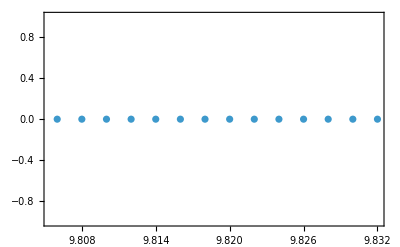

```mathematica
(*Find position and effective theory of TMS*)
ths=10^-2;
δe1=eigval1[[;;,;;,3]]-eigval1[[;;,;;,2]];
pos1=Position[Chop[δe1,ths],0];
curve1=Table[{j1arr[[pos1[[i,1]]]],j2arr[[pos1[[i,2]]]]},{i,1,Dimensions[pos1][[1]]}];
Length[curve1]
δe2=eigval2[[;;,;;,3]]-eigval2[[;;,;;,2]];
pos2=Position[Chop[δe2,ths],0];
curve2=Table[{j1arr[[pos2[[i,1]]]],j2arr[[pos2[[i,2]]]]},{i,1,Dimensions[pos2][[1]]}];


Show[ListPlot[curve1,
Frame->True,
LabelStyle->labstyle,
FrameLabel->{
MaTeX["J_1/\\bar{b}", Magnification -> magn] ,
MaTeX[" J_2/\\bar{b}", Magnification ->magn]
},
PlotLegends->Automatic,
ImageSize->IS],
ListPlot[curve2,
Frame->True,
LabelStyle->labstyle,
PlotStyle->Red,
FrameLabel->{
MaTeX["J_1/\\bar{b}", Magnification -> magn] ,
MaTeX[" J_2/\\bar{b}", Magnification ->magn]
},
PlotLegends->Automatic,
ImageSize->IS]
]
```

```mathematica
(*Find position and effective theory at XOSO*)
i1test=1;
i2test=1;
eigtot=KroneckerProduct[eigvect1[[pos1[[i1test,1]],pos1[[i1test,2]],2;;3]],eigvect2[[pos2[[i2test,1]],pos2[[i2test,2]],2;;3]]];
(*Find projected matrix onto computational subspace*)
Hmattot=KroneckerProduct[Hmat1/.{j1->curve1[[i1test,1]],j2->curve1[[i1test,2]]},IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],Hmat2/.{j1->curve2[[i2test,1]],j2->curve2[[i2test,2]]}];
Hdjtot=dj1 KroneckerProduct[Hdj1,IdentityMatrix[8]]+dj2 KroneckerProduct[IdentityMatrix[8],Hdj2];
HΣjtot=Σj1 KroneckerProduct[HΣj1,IdentityMatrix[8]]+Σj2 KroneckerProduct[IdentityMatrix[8],HΣj2];
(h0=eigtot*.Hmattot.eigtotᵀ//FullSimplify//Chop//FullSimplify)//MatrixForm
(hdj=eigtot*.Hdjtot.eigtotᵀ//FullSimplify//Chop//FullSimplify)//MatrixForm
(hΣj=eigtot*.HΣjtot.eigtotᵀ//FullSimplify//Chop//FullSimplify)//MatrixForm
(hint=Chop[eigtot*.Hint.eigtotᵀ//FullSimplify,ths]//Chop//FullSimplify)//MatrixForm
(*eigvect2[[pos2[[i2test,1]],pos2[[i2test,2]],2;;3]]*.Sztot.eigvect2[[pos2[[i2test,1]],pos2[[i2test,2]],2;;3]]ᵀ//Chop//FullSimplify//MatrixForm
eigvect1[[pos1[[i1test,1]],pos1[[i1test,2]],2;;3]]*.Sztot.eigvect1[[pos1[[i1test,1]],pos1[[i1test,2]],2;;3]]ᵀ//Chop//FullSimplify//MatrixForm*)
```

(-76.692 | 0 | 0 | 0
0 | -76.6838 | 0 | 0
0 | 0 | -76.6833 | 0
0 | 0 | 0 | -76.6751)

(0.5 dj1+0.5 dj2 | -0.252822 dj2 | -0.108349 dj1 | 0
-0.252822 dj2 | 0.5 dj1-0.808403 dj2 | 0 | -0.108349 dj1
-0.108349 dj1 | 0 | -0.68807 dj1+0.5 dj2 | -0.252822 dj2
0 | -0.108349 dj1 | -0.252822 dj2 | -0.68807 dj1-0.808403 dj2)

(0 | 0.252822 Σj2 | 0.108349 Σj1 | 0
0.252822 Σj2 | -0.564079 Σj2 | 0 | 0.108349 Σj1
0.108349 Σj1 | 0 | -0.235028 Σj1 | 0.252822 Σj2
0 | 0.108349 Σj1 | 0.252822 Σj2 | -0.235028 Σj1-0.564079 Σj2)

(-0.25 jsc+0.25 jss1-0.25 jss2+0.25 jss3+0.25 jss4 | 0 | 0 | 0
0 | -0.122162 jsc-0.25 jss1+0.122162 jss2-0.122162 jss3+0.122162 jss4 | 0 | 0
0 | 0 | 0.25 jsc-0.25 jss1+0.25 jss2-0.226521 jss3-0.226521 jss4 | 0
0 | 0 | 0 | 0.122162 jsc+0.25 jss1-0.122162 jss2+0.110689 jss3-0.110689 jss4)

```mathematica
Print["Single particle"]
testMatrix=h0+hdj+hΣj;
(*Decomposition grouped by term order*)
groupedDecomposition=DecomposeSpinOperators[testMatrix];
(*Output*)
groupedDecomposition
Print["interactions"]
testMatrix=hint;
(*Decomposition grouped by term order*)
groupedDecomposition=DecomposeSpinOperators[testMatrix];
(*Output*)
groupedDecomposition
```

Single particle

<|SingleQubitTerms→<|{I ⊗ σx,1}→-0.126411 dj2+0.126411 Σj2,{I ⊗ σz,1}→-0.00205571-1.38778×10^-17 dj1+0.327101 dj2-3.46945×10^-18 Σj1+0.14102 Σj2,{σx ⊗ I,1}→-0.0541745 dj1+0.0541745 Σj1,{σz ⊗ I,1}→-0.00216732+0.297017 dj1+1.38778×10^-17 dj2+0.058757 Σj1|>,TwoQubitTerms→<||>,ThreeQubitTerms→<||>|>

interactions

<|SingleQubitTerms→<|{I ⊗ σz,1}→0.+0.004369 jss3+0.00150076 jss4,{σz ⊗ I,1}→0.-0.0930405 jsc-0.0319595 jss2+0.0304587 jss3+0.0886715 jss4|>,TwoQubitTerms→<|{σz ⊗ σz,2}→-0.0319595 jsc+0.125 jss1-0.0930405 jss2+0.0886715 jss3+0.0304587 jss4|>,ThreeQubitTerms→<||>|>

```mathematica
(*leakage calculation*)
```

```mathematica
(*j1Q1=curve1[[i1test,1]]
j2Q1=curve1[[i1test,2]]
j1Q2=curve2[[i2test,1]]
j2Q2=curve2[[i2test,2]]

Jint=10;
Tmax=0.1;
Tarr=Table[t,{t,0,Tmax,0.005}];
narr=Tarr;

Hmat1XOSO=Hmat1/. {j1->j1Q1,j2->j2Q1};
Hmat2XOSO=Hmat2/. {j1->j1Q2,j2->j2Q2};

HintGate=Hint/. {jcc->0,jsc->0,jss1->0,jss2->0,jss3->Jint,jss4->0};

Hfull=KroneckerProduct[Hmat1XOSO,IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],Hmat2XOSO]+HintGate//N//Chop;

Ufull=ParallelTable[MatrixExp[-I Hfull t],{t,Tarr}];

compCardinal={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
compBell={{1,0,0,1}/Sqrt[2],{1,0,0,-1}/Sqrt[2],{0,1,1,0}/Sqrt[2],{0,1,-1,0}/Sqrt[2]};
arrtotcomp=Join[compCardinal,compBell];

eigtotMatrix=N[Transpose[eigtot]];

resultMatrix=eigtotMatrix.Transpose[arrtotcomp];
arrtotfull=Transpose[resultMatrix];

leakageCalc=ParallelTable[Ut=Ufull[[nind]];
Pcomp=eigtotMatrix.ConjugateTranspose[eigtotMatrix];
AvgLeakage=1/Length[arrtotcomp] Sum[psiInitialFull=arrtotfull[[i]];
V=Ut.Transpose[{psiInitialFull}];
probStay=ConjugateTranspose[V].Pcomp.V//First//Chop;
Re[Max[0,1-probStay]],{i,1,Length[arrtotcomp]}];
{narr[[nind]],AvgLeakage},{nind,1,Length[narr]}];

ListLogPlot[leakageCalc,Frame->True,FrameLabel->{"t [1/MHz]","Leakage (Average)"},PlotLabel->"Leakage of sigma\_z \\otimes sigma\_z Gate",ImageSize->Large,PlotRange->All]*)
```

```mathematica
(*ConjugateTranspose[eigtotMatrix].eigtotMatrix//Chop//MatrixForm*)
```

```mathematica
(*Pcomp=eigtotMatrix.ConjugateTranspose[eigtotMatrix];

Table[psi=arrtotfull[[i]];
v=Transpose[{psi}];
probStay0=ConjugateTranspose[v].Pcomp.v//First//Chop;
{i,probStay0},{i,Length[arrtotfull]}]*)
```

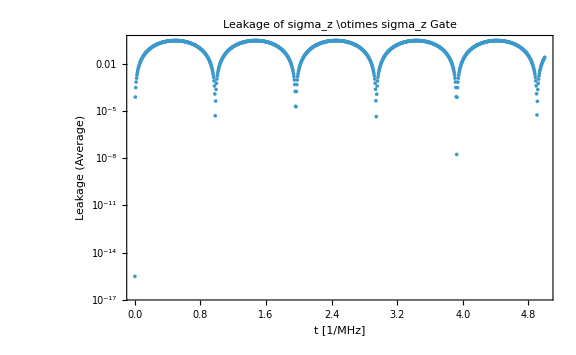

```mathematica
j1Q1=curve1[[i1test,1]];
j2Q1=curve1[[i1test,2]];
j1Q2=curve2[[i2test,1]];
j2Q2=curve2[[i2test,2]];

Jint=5.0;
Tmax=5;
Tarr=Table[t,{t,0,Tmax,0.005}];
narr=Tarr;
(*find idle hams to check the leakage*)
Hmat1XOSO=Hmat1/. {j1->j1Q1,j2->j2Q1};
Hmat2XOSO=Hmat2/. {j1->j1Q2,j2->j2Q2};

HintGate=Hint/. {jcc->0,jsc->0,jss1->Jint,jss2->0,jss3->0,jss4->0};

Hfull=KroneckerProduct[Hmat1XOSO,IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],Hmat2XOSO]+HintGate//N//Chop;

Ufull=ParallelTable[MatrixExp[-I Hfull t],{t,Tarr}];

compCardinal={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};

compBell={{1,0,0,1}/Sqrt[2],{1,0,0,-1}/Sqrt[2],{0,1,1,0}/Sqrt[2],{0,1,-1,0}/Sqrt[2]};

arrtotcomp=Join[compCardinal,compBell];

eigtotMatrix=N[Transpose[eigtot]];
Pcomp=eigtotMatrix.ConjugateTranspose[eigtotMatrix];

leakageCalc=ParallelTable[Ut=Ufull[[nind]];
AvgLeakage=1/Length[arrtotcomp] Sum[psiLogical=arrtotcomp[[i]];
psiInitialFull=eigtotMatrix.psiLogical;
state=Ut.psiInitialFull;
probStay=Conjugate[state].(Pcomp.state)//Chop;
Re[Max[0,1-probStay]],{i,1,Length[arrtotcomp]}];
{narr[[nind]],AvgLeakage},{nind,1,Length[narr]}];

ListLogPlot[leakageCalc,Frame->True,FrameLabel->{"t [1/MHz]","Leakage (Average)"},PlotLabel->"Leakage of sigma_z \\otimes sigma_z Gate",ImageSize->Large,PlotRange->All]
```

```mathematica
(*eigtotMatrix=N[Transpose[eigtot]];          (*64 x 4*)
Pcomp=eigtotMatrix.ConjugateTranspose[eigtotMatrix];  (*64 x 64*)
Id=IdentityMatrix[64]; (*look at the states nearby and how the exchange couple these nearby states to the logical space*)
Pperp=Id-Pcomp;
Hll=Pcomp.HintGate.Pcomp;        
Hle=Pcomp.HintGate.Pperp;        
Hel=Pperp.HintGate.Pcomp;        
Hee=Pperp.HintGate.Pperp;
Norm[Hll,"Frobenius"]
Norm[Hel,"Frobenius"]*)
```

```mathematica
(*Sort[Eigenvalues[Hfull]]*)
```

```mathematica
(*Sort[Eigenvalues[Hmat2XOSO]]
Sort[Eigenvalues[Hmat1XOSO]]*)
```

```mathematica
(*Plot[Sort[Eigenvalues[Hmat2/.{j2->0}]],{j1,0,100}]*)
```

```mathematica
(*Sztot=KroneckerProduct@@@Permutations[{id,σz,id}]/2//Total;
levelsWithSz[j1val_]:=Module[{vals,vecs,ord,valsS,szVals},{vals,vecs}=Sort[Eigensystem[Hmat2/. {j1->j1val,j2->0}]];
szVals=Table[Chop[ConjugateTranspose[vecs[[k]]].(Sztot.vecs[[k]])],{k,Length[vals]}];
{vals,szVals}];*)
```

```mathematica
(*j1min=0;
j1max=100;
dj1=1;

j1list=Range[j1min,j1max,dj1];


{vals0,vecs0}=Eigensystem[Hmat1/. {j1->0,j2->0}];

ord=Ordering[vals0];            

vals0s=vals0[[ord]];
vecs0s=vecs0[[ord]];

numLevels=Length[vals0s];


mzAt0=Chop@Table[Conjugate[vecs0s[[k]]].(Sztot.vecs0s[[k]]),{k,numLevels}];

(*again just looking at the levels and their mzs*)
valsJ=Table[Sort[Eigenvalues[Hmat1/. {j1->j,j2->0}]],{j,j1list}];

levelCurves=Table[Transpose[{j1list,valsJ[[All,n]]}],{n,1,numLevels}];

legends=Table[MaTeX["m_z = "<>ToString[mzAt0[[n]]]],{n,numLevels}];

ListLinePlot[levelCurves,Frame->True,FrameLabel->{MaTeX["J_1"],MaTeX["E"]},PlotLegends->Placed[LineLegend[legends],Right],ImageSize->Large]*)
```

```mathematica
Clear[Uideal]; (*ideal gate i got from the analytics code*) (*here i calculate  2q gate fidelity*)
statesCPhase={{0,0,0,1},(* |00>*){1/Sqrt[2],0,0,1/Sqrt[2]},(*(|00>+ |11>)/√2*){1/Sqrt[2],0,1/Sqrt[2],0},(*(|01>+ |11>)/√2*){1/Sqrt[2],1/Sqrt[2],0,0},(*(|10>+ |11>)/√2*){1/2,1/2,1/2,1/2}                   (* |++>*)};

Uideal[jss1_]:={{ⅇ^((ⅈ (264613-851 jss1) π)/(1702 √(16+jss1^2))),0,0,0},{0,-ⅇ^((ⅈ (257805+851 jss1) π)/(1702 √(16+jss1^2))),0,0},{0,0,-ⅇ^((ⅈ (271421+851 jss1) π)/(1702 √(16+jss1^2))),0},{0,0,0,ⅇ^((ⅈ (264613-851 jss1) π)/(1702 √(16+jss1^2)))}};


Clear[Hmat1XOSO,Hmat2XOSO,HidleFull];

Hmat1XOSO=Hmat1/. {j1->j1Q1,j2->j2Q1}//Chop;
Hmat2XOSO=Hmat2/. {j1->j1Q2,j2->j2Q2}//Chop; (*find idle hams*)

HidleFull=N[KroneckerProduct[Hmat1XOSO,IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],Hmat2XOSO]]//Chop;
Clear[Hss1Full]; (*2q idle*)

HintTemplate=Hint/. {jcc->0,jsc->0,jss2->0,jss3->0,jss4->0};

Hss1Full[jss_]:=N[HidleFull+(HintTemplate/. jss1->jss)]//Chop;

(*Clear[HdJ231,HdJ23Full,HdeltaFull];

HdJ231=D[Hmat1,j2]/. {j1->j1Q1,j2->j2Q1}//N;


HdJ23Full=KroneckerProduct[HdJ231,IdentityMatrix[8]];


HdeltaFull[dJ23_]:=HidleFull+dJ23 *HdJ23Full;
Hdeltaf
*)
Clear[t1,UfullPulse];

t1[jss1_]:=(2 *Pi)/(√(16+jss1^2));

UfullPulse[jss1_]:=Module[{U1,U2},U1=MatrixExp[-I Hss1Full[jss1] t1[jss1]]];
Clear[eigtotMatrix];
eigtotMatrix=N[Transpose[eigtot]];
Clear[gateFidelityFull];

gateFidelityFull[jss1_]:=Module[{U,Flist,psiL,psiTarget,psiFullInit,psiFullFin,psiOut},U=UfullPulse[jss1];
Flist=Table[psiL=statesCPhase[[k]];psiTarget=Uideal[jss1].psiL;psiFullInit=eigtotMatrix.psiL;psiFullFin=U.psiFullInit;psiOut=ConjugateTranspose[eigtotMatrix].psiFullFin;
Abs[Conjugate[psiTarget].psiOut]^2,{k,1,Length[statesCPhase]}];
Mean[Flist]];
```

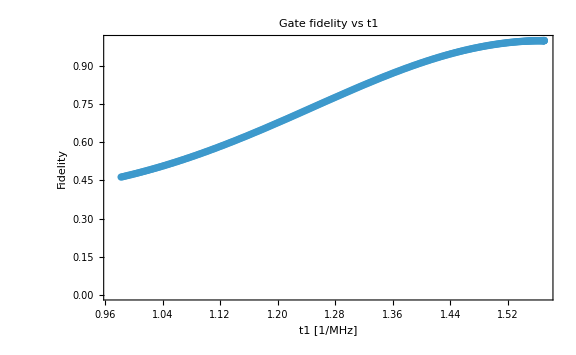

```mathematica
j1min=0.05;      
j1max=5.0;
dj1=0.02;


fidelityVsT1=Table[With[{τ1=t1[j1]},{τ1,gateFidelityFull[j1]}],{j1,j1min,j1max,dj1}];

ListPlot[fidelityVsT1,Frame->True,FrameLabel->{"t1  [1/MHz]","Fidelity"},PlotLabel->"Gate fidelity vs t1",PlotRange->{0,1},ImageSize->Large]
```

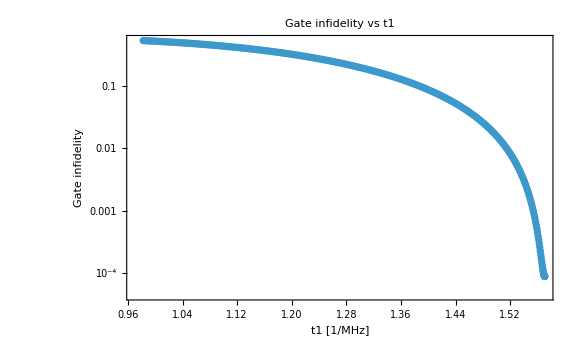

```mathematica
gateInfidelityFull[jss1_]:=1-gateFidelityFull[jss1]; (*plot infidelity instead of fiddelity*)

infidelityVsT1=Table[With[{τ1=t1[j1],inf=gateInfidelityFull[j1]},{τ1,inf}],{j1,j1min,j1max,dj1}];


infidelityVsT1clean=Select[infidelityVsT1,#[[2]]>0&];

ListLogPlot[infidelityVsT1clean,Frame->True,FrameLabel->{"t1 [1/MHz]","Gate infidelity"},PlotLabel->"Gate infidelity vs t1",ImageSize->Large]
```

```mathematica
Clear[HdJ12mat1,HdJ12mat2,HdJ12Full1,HdJ12Full2];

HdJ12mat1=D[Hmat1,j1]/. {j1->j1Q1,j2->j2Q1}//N;
HdJ12mat2=D[Hmat2,j1]/. {j1->j1Q2,j2->j2Q2}//N;

HdJ12Full1=KroneckerProduct[HdJ12mat1,IdentityMatrix[8]];
HdJ12Full2=KroneckerProduct[IdentityMatrix[8],HdJ12mat2];


(*now fidelity but let's generate some exchange noise*)

gateFidelitySample[jss1_,sigmaRel_:0.01]:=Module[{deltaSS,delta12a,delta12b,jssNoise,dJ12a,dJ12b,Hnoisy,U,Flist,psiL,psiTarget,psiFullInit,psiFullFin,psiOut},
deltaSS=RandomVariate[NormalDistribution[0,sigmaRel]];
delta12a=RandomVariate[NormalDistribution[0,sigmaRel]];
delta12b=RandomVariate[NormalDistribution[0,sigmaRel]];
jssNoise=jss1 (1+deltaSS);
dJ12a=j1Q1*(delta12a);
dJ12b=j1Q2 *delta12b;
Hnoisy=Hss1Full[jssNoise]+dJ12a HdJ12Full1+dJ12b HdJ12Full2;
U=MatrixExp[-I Hnoisy t1[jss1]];
Flist=Table[psiL=statesCPhase[[k]];
psiTarget=Uideal[jss1].psiL;
psiFullInit=eigtotMatrix.psiL;
psiFullFin=U.psiFullInit;
psiOut=ConjugateTranspose[eigtotMatrix].psiFullFin;
Abs[Conjugate[psiTarget].psiOut]^2,{k,1,Length[statesCPhase]}];
Mean[Flist]]
gateFidelityAveraged[jss1_,sigmaRel_:0.01,nsamp_:200]:=Mean@Table[gateFidelitySample[jss1,sigmaRel],{nsamp}];



jstar=0.5;
fClean=gateFidelityFull[jstar];
fNoisy=gateFidelityAveraged[jstar,0.001,500];
{fClean,fNoisy}
```

{0.99945,0.999283}

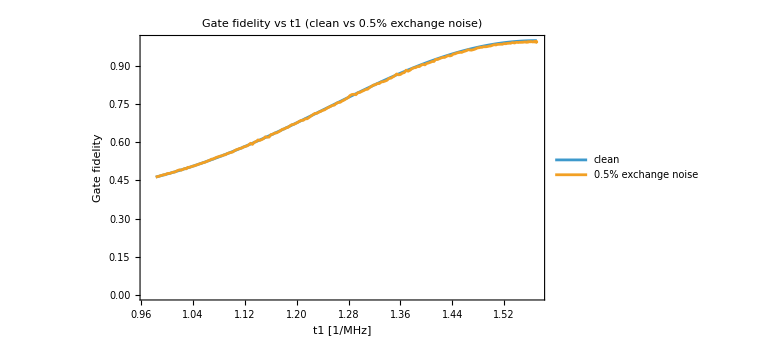

```mathematica
sigmaRel=0.005;   (*parameters for the quasistatic noise sample*)
nsamp=100;    

fidelityVsT1Clean=Table[{t1[j1],gateFidelityFull[j1]},{j1,j1min,j1max,dj1}];

fidelityVsT1Noisy=ParallelTable[{t1[j1],gateFidelityAveraged[j1,sigmaRel,nsamp]},{j1,j1min,j1max,dj1}];

ListPlot[{fidelityVsT1Clean,fidelityVsT1Noisy},Frame->True,FrameLabel->{"t1 [1/MHz]","Gate fidelity"},PlotLabel->"Gate fidelity vs t1 (clean vs 0.5% exchange noise)",PlotRange->{0,1},Joined->True,ImageSize->Large,PlotLegends->{"clean","0.5% exchange noise"}]
```

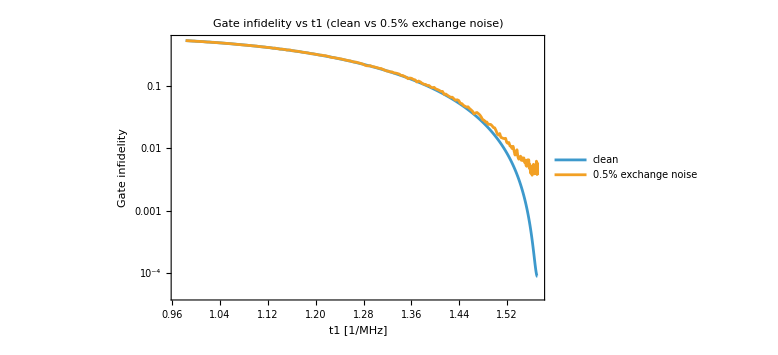

```mathematica
infidelityVsT1clean={#[[1]],1-#[[2]]}&/@(fidelityVsT1Clean);
infidelityVsT1Noisy={#[[1]],1-#[[2]]}&/@(fidelityVsT1Noisy); (*infidelity with noise*)

ListLogPlot[{infidelityVsT1clean,infidelityVsT1Noisy},Frame->True,FrameLabel->{"t1 [1/MHz]","Gate infidelity"},PlotLabel->"Gate infidelity vs t1 (clean vs 0.5% exchange noise)",Joined->True,ImageSize->Large,PlotLegends->{"clean","0.5% exchange noise"}]
```

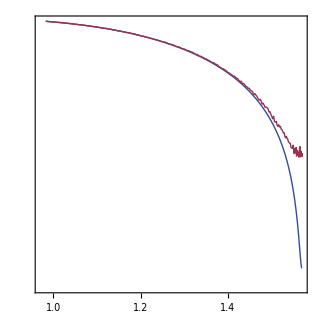

```mathematica
Needs["MaTeX`"];

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}","\\usepackage{lmodern}"}];
tex[s_,fs_:20]:=MaTeX[s,FontSize->fs];

niceColors={RGBColor[0.20,0.30,0.60],RGBColor[0.60,0.20,0.30]};

infidelityVsT1clean={#[[1]],1-#[[2]]}&/@fidelityVsT1Clean;
infidelityVsT1Noisy={#[[1]],1-#[[2]]}&/@fidelityVsT1Noisy;

(*ticks for a log10 y-axis:show only powers of 10 as 10^{n}*)
log10Ticks[min_,max_]:=Module[{a,b,exps},a=Floor[Log10[min]];
b=Ceiling[Log10[max]];
exps=Range[a,b];
Table[{10^e,tex["10^{"<>ToString[e]<>"}",16]},{e,exps}]];

inf=ListLogPlot[{infidelityVsT1clean,infidelityVsT1Noisy},Joined->True,PlotStyle->{Directive[Thick,niceColors[[1]]],Directive[Thick,niceColors[[2]]]},Frame->True,FrameStyle->Black,PlotRange->All,PlotRangeClipping->False,(* <--key change:custom left y ticks*)FrameTicks->{{log10Ticks[10^-5,1],None},(*left,right*){Automatic,None}              (*bottom,top*)},FrameTicksStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{tex["t_1\\,[\\mu s]",18],tex["\\text{Gate infidelity}",18]},PlotLabel->tex["\\sigma_z\\sigma_z^{\\prime}\\ \\text{gate}",18],GridLines->None,AspectRatio->1,ImageSize->320,ImagePadding->{{60,15},{50,20}},PlotLegends->Placed[LineLegend[{Directive[Thick,niceColors[[1]]],Directive[Thick,niceColors[[2]]]},{tex["\\text{clean}",18],tex["0.5\\%\\ \\text{noise}",18]},LegendMarkerSize->28,LegendLayout->"Column",LabelStyle->Directive[Black,FontFamily->"Times",18]],Scaled[{0.63,0.30}]]]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Downloads","infidelity_2q.pdf"}],inf]
```

C:\Users\tesya\Downloads\infidelity_2q.pdf

```mathematica
(*1q gate fidelities*)
```

```mathematica
Clear[gateFidelityFullz,tztarget,Hmat1XOSO,soltarJz];
j1Q1=curve1[[i1test,1]];
j2Q1=curve1[[i1test,2]];

Tmax=1;
Tarr=Table[t,{t,0.01,Tmax,0.005}];


Hmat1XOSO=Hmat1/. {j1->j1Q1-dJ12,j2->j2Q1+dJ23};
eiglog=eigvect1[[pos1[[i1test,1]],pos1[[i1test,2]],2;;3]];
states6={{1,0},{0,1},1/Sqrt[2] {1,1},1/Sqrt[2] {1,-1},1/Sqrt[2] {1,I},1/Sqrt[2] {1,-I}};
eiglogMatrix=N[Transpose[eiglog]];
g1t={g1->53,g2->74,g3->47(*MHz*)

};
hz=(dJ12 (g1+g2-2 g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))*PauliMatrix[3]/.g1t;
Uz[t_]:=MatrixExp[-I*hz*t]//FullSimplify
soltarz=First@Solve[hz[[1,1]]*t==Pi/4,t];
soltarJz[tg_]:=First@Solve[hz[[1,1]]*tg==Pi/4,dJ12]
Uztarget=Uz[-t]/.soltarz;
tztarget[dJ12_]:=soltarz[[1,2]];
Ufullz[tg_]:=MatrixExp[-I*Hmat1XOSO *tg/.dJ23->0/.soltarJz[tg]];
```

```mathematica
gateFidelityFullz[tg_]:=Module[{U,Flist,psiL,psiTarget,psiFullInit,psiFullFin,psiOut,Uf},U=Uztarget;Uf=Ufullz[tg];
Flist=Table[psiL=states6[[k]];psiTarget=U.psiL;psiFullInit=eiglogMatrix.psiL;psiFullFin=Uf.psiFullInit;psiOut=ConjugateTranspose[eiglogMatrix].psiFullFin;
Abs[Conjugate[psiTarget].psiOut]^2,{k,1,Length[states6]}];
Mean[Flist]];

leakageFullz[tg_]:=Module[{Flist,psiL,psiFullInit,psiFullFin,psiOut,Uf},Uf=Ufullz[tg];
Flist=Table[psiL=states6[[k]];
psiFullInit=eiglogMatrix.psiL;psiFullFin=Uf.psiFullInit;psiOut=ConjugateTranspose[eiglogMatrix].psiFullFin;
1-ConjugateTranspose[psiOut].psiOut,{k,1,Length[states6]}];
Mean[Flist]];
```

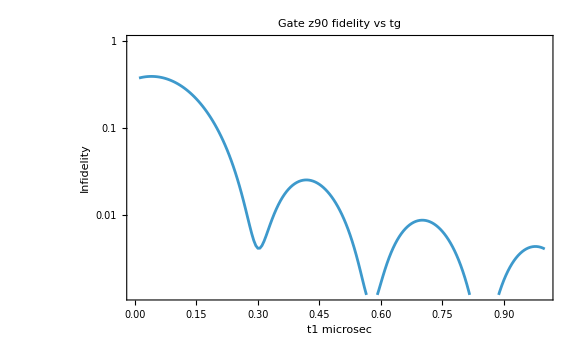

```mathematica
infidzVals=1-Table[gateFidelityFullz[tg],{tg,Tarr}];
leakagevals=Table[leakageFullz[tg],{tg,Tarr}];

infidzTable=Transpose[{Tarr,infidzVals}];
leakageTable=Transpose[{Tarr,leakagevals}];
ListLogPlot[infidzTable,Frame->True,Joined->True,FrameLabel->{"t1 microsec","Infidelity"},PlotLabel->"Gate z90 fidelity vs tg",PlotRange->{0,1},PlotRange->All]
```

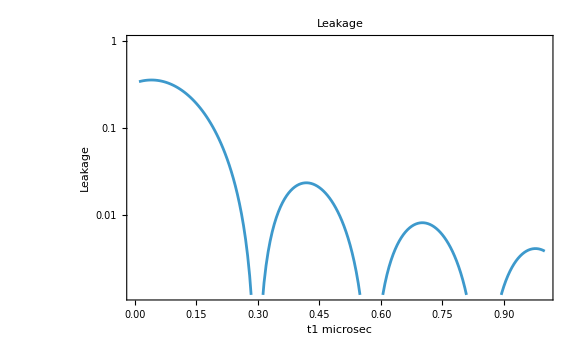

```mathematica
ListLogPlot[leakageTable,Frame->True,Joined->True,FrameLabel->{"t1 microsec","Leakage"},PlotLabel->"Leakage",PlotRange->{0,1},PlotRange->All]
```

Vlog^† Vlog =

(1. | 0
0 | 1.)

Plog^2 - Plog =

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

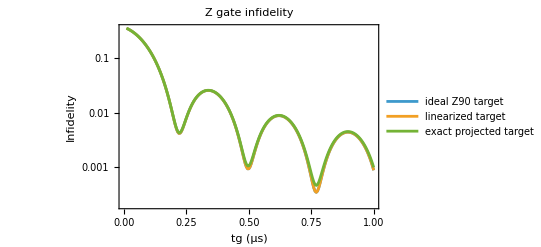

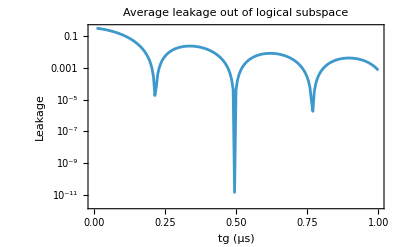

```mathematica
(* =========================================*)(*FIXED LOGICAL GATE/LEAKAGE CODE*)(* =========================================*)ClearAll[Vlog,Plog,Mfullz,leakageAvgz,gateFidelityAvgz,gateFidelity6Statez,Ufullz,Hfullz,HlogExactz,HlogExactTracelessz,hzLin,omegaZLin,dJ12ForZ90Linear,dJ12ForAngleLinear,UtargetIdealZ90,UtargetLinearZ,UtargetExactProjectedZ,states6,sanityVlog1,sanityVlog2,tg,dJ12,dJ23];

(*-----------------------------------------*)
(*1) Logical basis at idle point*)
(*-----------------------------------------*)

j1Q1=curve1[[i1test,1]];
j2Q1=curve1[[i1test,2]];

(*Take the two logical eigenvectors at the idle/degeneracy point*)
eiglog=eigvect1[[pos1[[i1test,1]],pos1[[i1test,2]],2;;3]];

(*Make them columns of an 8x2 matrix*)
Vlog=N[Transpose[eiglog]];

(*Projector onto logical subspace*)
Plog=Vlog.ConjugateTranspose[Vlog];

(*Sanity checks:must be identity/projector*)
sanityVlog1=Chop[ConjugateTranspose[Vlog].Vlog,10^-10];
sanityVlog2=Chop[Plog.Plog-Plog,10^-10];

Print["Vlog^† Vlog ="];
sanityVlog1//MatrixForm

Print["Plog^2 - Plog ="];
sanityVlog2//MatrixForm

(*-----------------------------------------*)
(*2) Six logical test states (optional)*)
(*-----------------------------------------*)

states6={{1,0},{0,1},1/Sqrt[2] {1,1},1/Sqrt[2] {1,-1},1/Sqrt[2] {1,I},1/Sqrt[2] {1,-I}};

(*-----------------------------------------*)
(*3) Full 8x8 Hamiltonian during pulse*)
(*-----------------------------------------*)

Hfullz[dj12_?NumericQ,dj23_:0]:=N[Hmat1/. {j1->j1Q1+dj12,j2->j2Q1+dj23}];

Ufullz[tg_?NumericQ,dj12_?NumericQ,dj23_:0]:=MatrixExp[-I*Hfullz[dj12,dj23]*tg];

(*-----------------------------------------*)
(*4) Effective 2x2 map on logical subspace*)
(*-----------------------------------------*)

Mfullz[tg_?NumericQ,dj12_?NumericQ,dj23_:0]:=Module[{U},U=Ufullz[tg,dj12,dj23];
Chop[ConjugateTranspose[Vlog].U.Vlog,10^-12]];

(*-----------------------------------------*)
(*5) Leakage:standard average leakage*)
(*-----------------------------------------*)

leakageAvgz[tg_?NumericQ,dj12_?NumericQ,dj23_:0]:=Module[{M},M=Mfullz[tg,dj12,dj23];
Re[1-Tr[ConjugateTranspose[M].M]/2]];

(*-----------------------------------------*)
(*6) Standard average gate fidelity*)
(*including leakage*)
(*-----------------------------------------*)

gateFidelityAvgz[tg_?NumericQ,dj12_?NumericQ,Utarget_?MatrixQ,dj23_:0]:=Module[{M},M=Mfullz[tg,dj12,dj23];
Re[(Tr[ConjugateTranspose[M].M]+Abs[Tr[ConjugateTranspose[Utarget].M]]^2)/6]];

(*-----------------------------------------*)
(*7) Optional old-style 6-state fidelity*)
(*as a sanity check*)
(*-----------------------------------------*)

gateFidelity6Statez[tg_?NumericQ,dj12_?NumericQ,Utarget_?MatrixQ,dj23_:0]:=Module[{Uf,Flist,psiL,psiTarget,psiFullInit,psiFullFin,psiOut},Uf=Ufullz[tg,dj12,dj23];
Flist=Table[psiL=states6[[k]];
psiTarget=Utarget.psiL;
psiFullInit=Vlog.psiL;
psiFullFin=Uf.psiFullInit;
psiOut=ConjugateTranspose[Vlog].psiFullFin;
Abs[Conjugate[psiTarget].psiOut]^2,{k,1,Length[states6]}];
Mean[Flist]];

(*-----------------------------------------*)
(*8) Three target choices*)
(*-----------------------------------------*)

(*8a) Ideal pure Z(pi/2):diag(e^{-i pi/4},e^{+i pi/4})*)
UtargetIdealZ90=MatrixExp[-I (Pi/4) PauliMatrix[3]];

(*8b) Linearized logical Hamiltonian near idle*)
g1t={g1->53,g2->74,g3->47(*MHz*)

};

hzLin[dj12_]:=N[((dj12 (g1+g2-2 g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))) PauliMatrix[3]/. g1t];

omegaZLin=Chop[hzLin[1.0][[1,1]],10^-14];
(*since hzLin[dj12]=dj12*omegaZLin*sigma_z*)

(*choose dj12 so that linearized theory gives Z(pi/2) in time tg*)
dJ12ForZ90Linear[tg_?NumericQ]:=N[(Pi/4)/(omegaZLin*tg)];

(*more general:choose dj12 for arbitrary angle phi,U=exp[-i (phi/2) sigma_z]*)
dJ12ForAngleLinear[tg_?NumericQ,phi_?NumericQ]:=N[(phi/2)/(omegaZLin*tg)];

UtargetLinearZ[tg_?NumericQ,dj12_?NumericQ]:=MatrixExp[-I hzLin[dj12] tg];

(*8c) Exact projected plateau Hamiltonian in idle basis*)
HlogExactz[dj12_?NumericQ,dj23_:0]:=Module[{H},H=Hfullz[dj12,dj23];
Chop[ConjugateTranspose[Vlog].H.Vlog,10^-12]];

(*Remove irrelevant identity part*)
HlogExactTracelessz[dj12_?NumericQ,dj23_:0]:=Module[{H2},H2=HlogExactz[dj12,dj23];
Chop[H2-(Tr[H2]/2) IdentityMatrix[2],10^-12]];

UtargetExactProjectedZ[tg_?NumericQ,dj12_?NumericQ,dj23_:0]:=MatrixExp[-I HlogExactTracelessz[dj12,dj23] tg];

(*-----------------------------------------*)
(*9) Recommended usage modes*)
(*-----------------------------------------*)

(*Mode A:compare to ideal Z(pi/2),choosing dj12 from linear theory*)
FidIdealZ90[tg_?NumericQ]:=Module[{dj12},dj12=dJ12ForZ90Linear[tg];
gateFidelityAvgz[tg,dj12,UtargetIdealZ90,0]];

LeakIdealZ90[tg_?NumericQ]:=Module[{dj12},dj12=dJ12ForZ90Linear[tg];
leakageAvgz[tg,dj12,0]];

(*Mode B:compare full evolution to linearized target*)
FidLinearTarget[tg_?NumericQ]:=Module[{dj12,Ut},dj12=dJ12ForZ90Linear[tg];
Ut=UtargetLinearZ[tg,dj12];
gateFidelityAvgz[tg,dj12,Ut,0]];

(*Mode C:compare full evolution to exact projected plateau gate-- this removes the "linear target is lying" issue*)
FidExactProjectedTarget[tg_?NumericQ]:=Module[{dj12,Ut},dj12=dJ12ForZ90Linear[tg];
Ut=UtargetExactProjectedZ[tg,dj12,0];
gateFidelityAvgz[tg,dj12,Ut,0]];

(*Optional:old 6-state version for sanity*)
Fid6StateIdealZ90[tg_?NumericQ]:=Module[{dj12},dj12=dJ12ForZ90Linear[tg];
gateFidelity6Statez[tg,dj12,UtargetIdealZ90,0]];

(*-----------------------------------------*)
(*10) Example scan*)
(*-----------------------------------------*)

Tmax=1.0;
Tarr=Table[t,{t,0.01,Tmax,0.005}];

infidIdealVals=1-Table[FidIdealZ90[tg],{tg,Tarr}];
infidLinearVals=1-Table[FidLinearTarget[tg],{tg,Tarr}];
infidExactProjVals=1-Table[FidExactProjectedTarget[tg],{tg,Tarr}];
leakageVals=Table[LeakIdealZ90[tg],{tg,Tarr}];

infidIdealTable=Transpose[{Tarr,infidIdealVals}];
infidLinearTable=Transpose[{Tarr,infidLinearVals}];
infidExactProjTable=Transpose[{Tarr,infidExactProjVals}];
leakageTable=Transpose[{Tarr,leakageVals}];

ListLogPlot[{infidIdealTable,infidLinearTable,infidExactProjTable},Frame->True,Joined->True,FrameLabel->{"tg (μs)","Infidelity"},PlotLabel->"Z gate infidelity",PlotLegends->{"ideal Z90 target","linearized target","exact projected target"},PlotRange->All]

ListLogPlot[leakageTable,Frame->True,Joined->True,FrameLabel->{"tg (μs)","Leakage"},PlotLabel->"Average leakage out of logical subspace",PlotRange->All]
```

Vlog^† Vlog =

(1. | 0
0 | 1.)

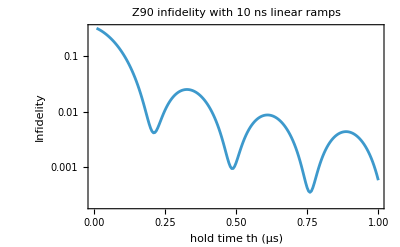

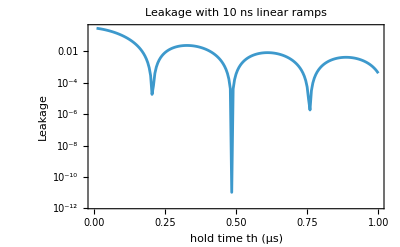

```mathematica
(* =========================================*)(*LINEAR RAMP UP/HOLD/RAMP DOWN*)(* =========================================*)ClearAll[dJ12Pulse,dJ23Pulse,HpulseZ,UfullRampZ,MfullRampZ,leakageRampZ,fidelityRampZ,fidelity6RampZ,TarrHold,tr,dt,th];

(*ramp time in microseconds:10 ns=0.01 us*)
tr=0.01;

(*time step in microseconds;make smaller if needed*)
dt=0.0005;   (*0.5 ns*)

(*use same idle logical basis as before*)
j1Q1=curve1[[i1test,1]];
j2Q1=curve1[[i1test,2]];

eiglog=eigvect1[[pos1[[i1test,1]],pos1[[i1test,2]],2;;3]];
Vlog=N[Transpose[eiglog]];
Plog=Vlog.ConjugateTranspose[Vlog];

Print["Vlog^† Vlog ="];
Chop[ConjugateTranspose[Vlog].Vlog,10^-10]//MatrixForm

(*same 6 logical test states*)
states6={{1,0},{0,1},1/Sqrt[2] {1,1},1/Sqrt[2] {1,-1},1/Sqrt[2] {1,I},1/Sqrt[2] {1,-I}};

(*-----------------------------------------*)
(*target amplitude from linearized Z model*)
(*-----------------------------------------*)

g1t={g1->53,g2->74,g3->47(*MHz*)

};

hzLin[dj12_]:=N[((dj12 (g1+g2-2 g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))) PauliMatrix[3]/. g1t];

omegaZLin=Chop[hzLin[1.0][[1,1]],10^-14];

(*choose plateau amplitude so that HOLD PART ONLY gives Z(pi/2)*)
dJ12ForZ90Hold[th_?NumericQ]:=N[(Pi/4)/(omegaZLin*th)];

(*ideal target*)
UtargetIdealZ90=MatrixExp[-I (Pi/4) PauliMatrix[3]];

(*-----------------------------------------*)
(*pulse shape:linear ramp up,hold,down*)
(*total duration T=th+2 tr*)
(*plateau amplitude=dj12Max*)
(*-----------------------------------------*)

dJ12Pulse[t_?NumericQ,th_?NumericQ,dj12Max_?NumericQ]:=Piecewise[{{dj12Max (t/tr),0<=t<tr},{dj12Max,tr<=t<tr+th},{dj12Max (1-(t-tr-th)/tr),tr+th<=t<=2 tr+th}},0];

(*keep dJ23=0 for your Z direction*)
dJ23Pulse[t_?NumericQ,th_?NumericQ,dj23Max_:0]:=0;

HpulseZ[t_?NumericQ,th_?NumericQ,dj12Max_?NumericQ,dj23Max_:0]:=N[Hmat1/. {j1->j1Q1+dJ12Pulse[t,th,dj12Max],j2->j2Q1+dJ23Pulse[t,th,dj23Max]}];

(*-----------------------------------------*)
(*time-ordered evolution by small steps*)
(*-----------------------------------------*)

UfullRampZ[th_?NumericQ,dj12Max_?NumericQ,dj23Max_:0,dtStep_:dt]:=Module[{Ttot,tgrid,U=IdentityMatrix[Length[Hmat1]],Hmid,k,tmid},Ttot=2 tr+th;
tgrid=Range[0,Ttot,dtStep];
If[Last[tgrid]<Ttot,tgrid=Join[tgrid,{Ttot}]];
For[k=1,k<Length[tgrid],k++,tmid=(tgrid[[k]]+tgrid[[k+1]])/2;
Hmid=HpulseZ[tmid,th,dj12Max,dj23Max];
U=MatrixExp[-I Hmid (tgrid[[k+1]]-tgrid[[k]])].U;];
Chop[U,10^-12]];

(*-----------------------------------------*)
(*projected 2x2 map*)
(*-----------------------------------------*)

MfullRampZ[th_?NumericQ,dj12Max_?NumericQ,dj23Max_:0,dtStep_:dt]:=Module[{U},U=UfullRampZ[th,dj12Max,dj23Max,dtStep];
Chop[ConjugateTranspose[Vlog].U.Vlog,10^-12]];

(*-----------------------------------------*)
(*average leakage*)
(*-----------------------------------------*)

leakageRampZ[th_?NumericQ,dj12Max_?NumericQ,dj23Max_:0,dtStep_:dt]:=Module[{M},M=MfullRampZ[th,dj12Max,dj23Max,dtStep];
Re[1-Tr[ConjugateTranspose[M].M]/2]];

(*-----------------------------------------*)
(*average gate fidelity incl leakage*)
(*-----------------------------------------*)

fidelityRampZ[th_?NumericQ,dj12Max_?NumericQ,Utarget_?MatrixQ,dj23Max_:0,dtStep_:dt]:=Module[{M},M=MfullRampZ[th,dj12Max,dj23Max,dtStep];
Re[(Tr[ConjugateTranspose[M].M]+Abs[Tr[ConjugateTranspose[Utarget].M]]^2)/6]];

(*optional old 6-state check*)
fidelity6RampZ[th_?NumericQ,dj12Max_?NumericQ,Utarget_?MatrixQ,dj23Max_:0,dtStep_:dt]:=Module[{Uf,Flist,psiL,psiTarget,psiFullInit,psiFullFin,psiOut},Uf=UfullRampZ[th,dj12Max,dj23Max,dtStep];
Flist=Table[psiL=states6[[k]];
psiTarget=Utarget.psiL;
psiFullInit=Vlog.psiL;
psiFullFin=Uf.psiFullInit;
psiOut=ConjugateTranspose[Vlog].psiFullFin;
Abs[Conjugate[psiTarget].psiOut]^2,{k,1,Length[states6]}];
Mean[Flist]];

(* =========================================*)
(*CHOOSE plateau amplitude*)
(* =========================================*)

dj12FromHold[th_?NumericQ]:=N[(Pi/4)/(omegaZLin (th+tr))];

(*if you want,you can later improve this by calibrating on the full ramped pulse,but start with this*)

(* =========================================*)
(*SCAN vs hold time*)
(* =========================================*)

TarrHold=Table[t,{t,0.01,1.0,0.005}];

infidRampVals=Table[Module[{dj12Max},dj12Max=dj12FromHold[th];
1-fidelityRampZ[th,dj12Max,UtargetIdealZ90,0,dt]],{th,TarrHold}];

leakageRampVals=Table[Module[{dj12Max},dj12Max=dj12FromHold[th];
leakageRampZ[th,dj12Max,0,dt]],{th,TarrHold}];

infidRampTable=Transpose[{TarrHold,infidRampVals}];
leakageRampTable=Transpose[{TarrHold,leakageRampVals}];

ListLogPlot[infidRampTable,Frame->True,Joined->True,FrameLabel->{"hold time th (μs)","Infidelity"},PlotLabel->"Z90 infidelity with 10 ns linear ramps",PlotRange->All]

ListLogPlot[leakageRampTable,Frame->True,Joined->True,FrameLabel->{"hold time th (μs)","Leakage"},PlotLabel->"Leakage with 10 ns linear ramps",PlotRange->All]
```